# DECONVOLUTION

## ELE 489: DIGITAL SIGNAL PROCESSING LABORATORY

Due date:

## Introduction

Smoothing or blurring of signals is a commonly occurring mostly undesirable phenomenon and there is great interest and a lot research on how to undo some if not all of such degradation.

In this experiment we wish to tackle the following elementary problem. Given two finite-length sequences y and h, where the former is the result of a convolution between some unknown sequence x and the known sequence h, the goal is to calculate x. In other words, we wish to undo the convolution operation that converted sequence x into y and thus this is not surprisingly called deconvolution.

That this can be done is easy to see. Starting with convolution and a short sequence h={h_1,h_2,h_3}:

y_n =∑_(k=1)^3 h_k x_(n-k+1)	for n=1,2,3,...

Expanding, we get the first transient output sample as follows:

y_1 =h_1 x_1

From which we immediately get

x_1=y_1/h_1

Then, the second transient output sample is:

y_2 =h_1 x_2+h_2 x_1

And now we can solve for the unknown x_2 (since we already know x_1):

x_2=(y_2-h_2 x_1)/h_1

Continuing for one more step we get:

y_3=h_1 x_3+h_2 x_2+h_3 x_1

From which we get:

x_3=(y_3-h_2 x_2-h_3 x_1)/h_1

This process can be continued for all the remaining values of y.

## Problem 1. Code development

Implement the deconvolution calculation using structural programming constructs such as nested Do or For loops only.

### Requirements

Document your program, explaining all relevant details of the code. Use short sequences and your convolve function from Laboratory 1 to obtain the samples of y which to use to reconstruct samples of x. Test your program by comparing with known results, for example by verifying with hand calculations. Also, clearly, the convolution of sequence x with h should yield y. Include this as one of your tests.

The fully functional and tested code should be encapsulated in the WL Module construct with the following function name and arguments:

deconvolve[y,h]

where y and h are two lists (vectors) such that Length[y]≥ Length[h].

## Problem 2.

Deconvolve the sequence shown below using the following filter h:

```mathematica
h={1,1,1,1,1,1,1}/7.;
```

This defines sequence y:

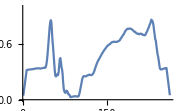

```mathematica
y=;
ListLinePlot[y,PlotRange->{0,1},ImageSize->Small]
```

## Problem 3.

Perfect reconstruction is only possible if the distortion, meaning the convolution filter h, is known exactly. However, in practice this is never the case. This is when deconvolution becomes an interesting problem.

In this problem reconstruct the signal in Problem 2 using the following and comment on the results. Do any of the following return a result that is close to the original x? Which one gives the best result? Anything surprising to note?

```mathematica
h1={1,1,1,1,1}/5.;
```

```mathematica
h2={0.95,1,1,1,1,1,0.95}/7.;
```

```mathematica
h3={0.85,1,1,1,1,1,0.85}/7.;
```

```mathematica
h4={0.5,1,1,1,1,1,0.5}/7.;
```

```mathematica
h5=GaussianMatrix[{{2}}]
```

{0.0508822,0.211838,0.474559,0.211838,0.0508822}